```mathematica
SetDirectory@NotebookDirectory[];
Import["QuESTlink.m"];
CreateLocalQuESTEnv["quest_link"];
```

## Parameters

```mathematica
model=3;(*3:Coher;*)
numQb=6;
numGt=numQb^2;
seed=-1;
ϵ=0.02;
SamSize=10000;
```

```mathematica
CreateFile["CS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>".dat"];
file=File["CS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>".dat"];
Data={};
AppendTo[Data,"model:"<>ToString[model]];
AppendTo[Data,"numQb:"<>ToString[numQb]];
AppendTo[Data,"numGt:"<>ToString[numGt]];
AppendTo[Data,"seed:"<>ToString[seed]];
AppendTo[Data,"eps:"<>ToString[ϵ]];
AppendTo[Data,"SamSize:"<>ToString[SamSize]];
AppendTo[Data,""];
Export[file,Data];
```

CreateFile::filex: /Users/yl_gscaep/Nutstore Files/Folder_temp/Clifford_sampling/NS/CS_remote/CS-m3-Q6-G36-e0.02.dat already exists.

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Gates

```mathematica
PZ={{1.,0.},{0.,-1.}};
PX={{0.,1.},{1.,0.}};
PY={{0.,-ⅈ},{ⅈ,0.}};
iden=IdentityMatrix[2];
Clifford={iden,PX,PY,PZ,(iden+ⅈ PX)/Sqrt[2],(iden-ⅈ PX)/Sqrt[2],(iden+ⅈ PY)/Sqrt[2],(iden-ⅈ PY)/Sqrt[2],(iden+ⅈ PZ)/Sqrt[2],(iden-ⅈ PZ)/Sqrt[2],(PX+PY)/Sqrt[2],(PX-PY)/Sqrt[2],(PX+PZ)/Sqrt[2],(PX-PZ)/Sqrt[2],(PY+PZ)/Sqrt[2],(PY-PZ)/Sqrt[2],(ⅈ iden+PX+PY+PZ)/2,(ⅈ iden-PX-PY+PZ)/2,(ⅈ iden+PX-PY-PZ)/2,(ⅈ iden-PX+PY-PZ)/2,(-ⅈ iden+PX+PY+PZ)/2,(-ⅈ iden-PX-PY+PZ)/2,(-ⅈ iden+PX-PY-PZ)/2,(-ⅈ iden-PX+PY-PZ)/2};
```

```mathematica
gates=Table[IdentityMatrix[2],numQb+2*numGt];
```

## Circuits

```mathematica
GateGraphGen[numQb_,numGt_,seed_]:=(
GateGraph={};
If[seed==-1,
depth=Ceiling[numGt/Floor[numQb/2]];
qINI=0;
Do[(
Do[(
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+1,numQb]];
),{q,qINI,numQb-1,2}];
qINI=1-qINI;
),{t,0,depth-1,1}];
AppendTo[GateGraph,Table[0,numQb-1]]
];
If[seed!=-1,
SeedRandom[seed];
Do[(
q=RandomInteger[{0,numQb-1}];
dis=RandomInteger[{1,numQb-1}];
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+dis,numQb]];
),{t,0,numGt-1,1}];
AppendTo[GateGraph,RandomInteger[{0,1},numQb-1]]
];
Return[GateGraph]
)
GateGraph=GateGraphGen[numQb,numGt,seed]
```

{0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,{0,0,0,0,0}}

```mathematica
circuitIdeal[numQb_,numGt_,GateGraph_,gates_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

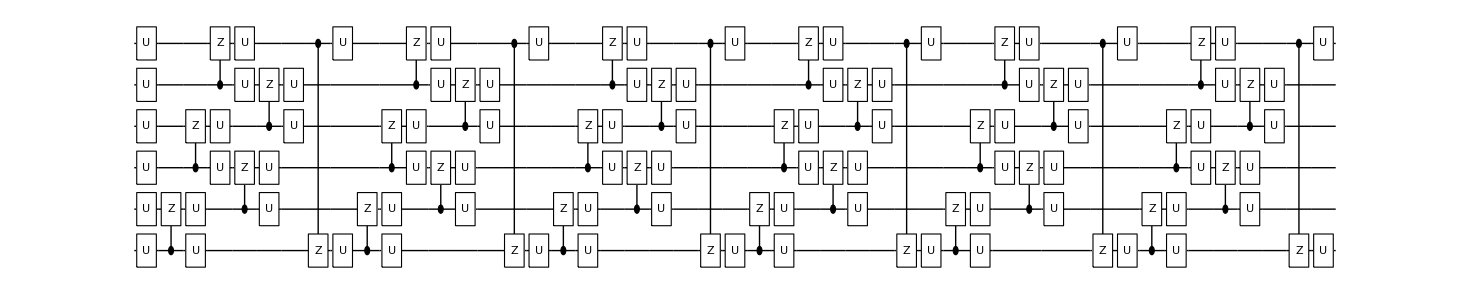

```mathematica
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
DrawCircuit@circI
```

```mathematica
circuitNoisy[numQb_,numGt_,GateGraph_,gates_,model_,ϵ_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];
AppendTo[circ,Subscript[Rz, q1][2*N[π,12]*ϵ]];AppendTo[circ,Subscript[Rz, q2][2*N[π,12]*ϵ]];
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

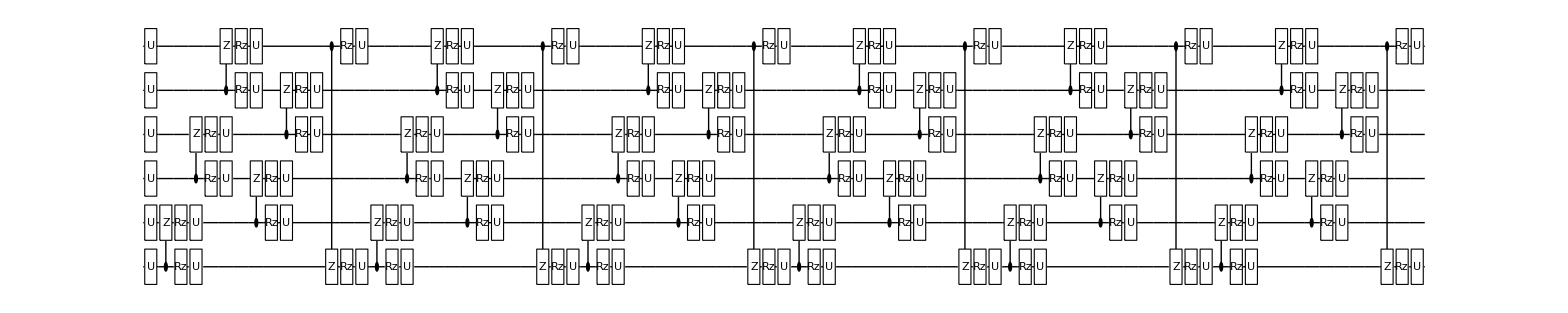

```mathematica
circN=circuitNoisy[numQb,numGt,GateGraph,gates,model,ϵ];
DrawCircuit@circN
```

## Sampling

```mathematica
SamplingU[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
Err={};
Fid={};
Do[(
gates=RandomVariate[CircularUnitaryMatrixDistribution[2],numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circNp=circuitNoisy[numQb,numGt,GateGraph,gates,model,ϵ];
circNn=circuitNoisy[numQb,numGt,GateGraph,gates,model,-ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circNp,ρIN,ρOUT];
ZNp=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
Fp=CalcFidelity[ρOUT,ψOUT];
ApplyCircuit[circNn,ρIN,ρOUT];
ZNn=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
Fn=CalcFidelity[ρOUT,ψOUT];
AppendTo[Err,(ZNp+ZNn)/2-ZI];
AppendTo[Fid,1-(Fp+Fn)/2];
),SamSize];
Return[{Err,Fid}]
)
```

```mathematica
SamplingC[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
Err={};
Fid={};
Do[(
gates=RandomChoice[Clifford,numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circNp=circuitNoisy[numQb,numGt,GateGraph,gates,model,ϵ];
circNn=circuitNoisy[numQb,numGt,GateGraph,gates,model,-ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circNp,ρIN,ρOUT];
ZNp=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
Fp=CalcFidelity[ρOUT,ψOUT];
ApplyCircuit[circNn,ρIN,ρOUT];
ZNn=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
Fn=CalcFidelity[ρOUT,ψOUT];
AppendTo[Err,(ZNp+ZNn)/2-ZI];
AppendTo[Fid,1-(Fp+Fn)/2];
),SamSize];
Return[{Err,Fid}]
)
```

## Simulation

Tue 18 Feb 2020 15:51:20GMT+8.

{0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,{0,0,0,0,0}}

Tue 18 Feb 2020 15:51:21GMT+8.

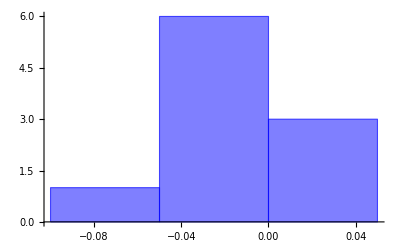

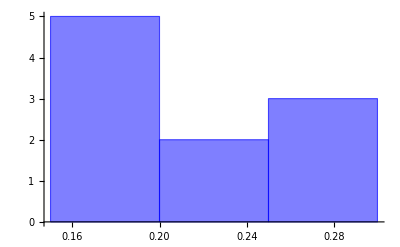

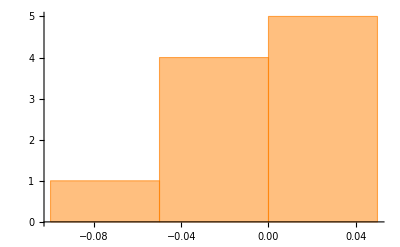

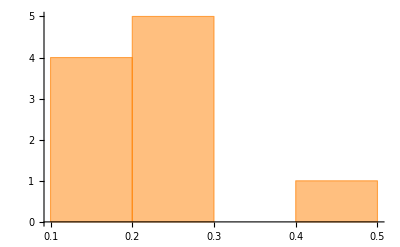

```mathematica
StartTime = Now
GateGraph=GateGraphGen[numQb,numGt,seed]
US=SamplingU[numQb,numGt,GateGraph,model,ϵ,SamSize];
CS=SamplingC[numQb,numGt,GateGraph,model,ϵ,SamSize];
EndTime = Now

Histogram[US[[1]],ChartStyle->Opacity[.5,Blue]]
Histogram[US[[2]],ChartStyle->Opacity[.5,Blue]]
Histogram[CS[[1]],ChartStyle->Opacity[.5,Orange]]
Histogram[CS[[2]],ChartStyle->Opacity[.5,Orange]]

AppendTo[Data,"US-Err:"];AppendTo[Data,US[[1]]];AppendTo[Data,""];
AppendTo[Data,"US-Fid:"];AppendTo[Data,US[[2]]];AppendTo[Data,""];
AppendTo[Data,"CS-Err:"];AppendTo[Data,CS[[1]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid:"];AppendTo[Data,CS[[2]]];AppendTo[Data,""];
AppendTo[Data,"Start Time: "<>ToString[StartTime]];
AppendTo[Data,"End Time: "<>ToString[EndTime]];
Export[file,Data];
```

```mathematica
MUS=Table[Moment[US[[1]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[1]],m],{m,1,10,1}]
MUS=Table[Moment[US[[2]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[2]],m],{m,1,10,1}]
```

{-0.0110135,0.00115908,-0.0000259419,3.24237×10^-6,-1.41396×10^-7,1.28233×10^-8,-7.46235×10^-10,5.76254×10^-11,-3.74864×10^-12,2.71544×10^-13}

{-0.0038825,0.00051335,-0.0000133116,8.0901×10^-7,-3.44652×10^-8,1.82676×10^-9,-8.86367×10^-11,4.55305×10^-12,-2.28622×10^-13,1.16569×10^-14}

{0.222504,0.0512626,0.0122047,0.0029936,0.00075375,0.000194079,0.0000509195,0.0000135691,3.66262×10^-6,9.9915×10^-7}

{0.232186,0.0601368,0.0173311,0.00550859,0.001901,0.000698863,0.000268798,0.000106603,0.0000431378,0.0000176843}